```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["SQLite"];
conn = OpenSQLConnection[JDBC["SQLite", "/Users/erinhengel/Dropbox/Readability/dta/read.db"]];
font="Optima";
```

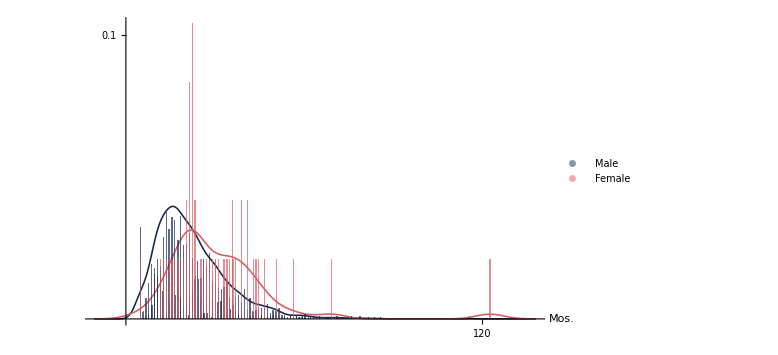

```mathematica
sql="
SELECT
	(JULIANDAY(Accepted) - JULIANDAY(Received)) / 30 AS ReviewLength,
	1 - AVG(Sex) AS FemRatio
		FROM Article
		NATURAL JOIN AuthorCorr
		NATURAL JOIN Author
	WHERE Received IS NOT NULL
	GROUP BY ArticleID;
";
data= SQLExecute[conn, sql];
male=Select[data,#⟦2⟧==0&]⟦All,1⟧;
female=Select[data,#⟦2⟧==1&]⟦All,1⟧;
opacity=Opacity[0.7];
{blue,pink}={RGBColor[26/255,40/255,78/255],RGBColor[216/255,92/255,99/255]};
legend=PointLegend[{blue,pink},{"Male","Female"},
LegendMarkers->Graphics[{EdgeForm[None],Opacity[0.5],Disk[]}],
LegendMarkerSize->10,
LabelStyle->{FontSize->16,FontColor->Gray,FontFamily->font},
LegendMargins->5,
LegendLayout->"Row"
];
kernel=SmoothHistogram[{male,female},
PlotStyle->{
{blue,Thickness[0.002]},
{pink,Thickness[0.002]}
},
AxesOrigin->{-5,0},
AxesStyle->Directive[Thin,Gray,FontFamily->font,FontSize->Medium],
Ticks->{{120},{0.1}}
];
histogram=Histogram[{male,female},{0.1},"Probability",
ChartStyle->{
Directive[blue,opacity],
Directive[pink,opacity]},
ChartLegends->Placed[legend,{Right,Center}]
];
plot=Show[
{kernel,histogram},
PlotRange->All,
AxesLabel->{"Mos.",None},
LabelStyle->{FontSize->14},
ImageSize->Full
];
Export["/Users/erinhengel/Dropbox/Readability/draft/pdf/figure5.pdf",plot];
Show[plot,ImageSize->Large]
```